## 1. 定义

### 1.1 必要准备

```mathematica
SetDirectory[NotebookDirectory[]];
$Assumptions=l∈ Integers&& m ∈Integers&&l>m&&l>10&&m>10&&f[r]>0&&l-m>8;
Needs["Instrumentation`"];
<<"Il_result.mx";(*Il*)
<<"Il0_result.mx";(*Il0*)
<<"CiMuNu_result.mx";(*CiMuNu*)
<<"clTPhi_result.mx";(*clTPhi*)
<<"csT_result.mx";(*csTPsi*)
Subscript[Φ, l_,m_] :=2 √(π/(2l+1)) ⅇ^(ⅈ m ((r0 ur ℒ Δr)/((-2 M+r0) (r0^2+ℒ^2))-ϕ0)) WignerD[{l,m,0},π,π/2,π/2] * Il0;
Subscript[ψ, l_,m_]:=2 √(π/(2l+1))ⅇ^(ⅈ m ((r0 ur ℒ Δr)/((-2 M+r0) (r0^2+ℒ^2))-ϕ0)) WignerD[{l,m,0},π,π/2,π/2];
Subscript[psi, l,m] = Flatten[Il/.{e->ℰ,L->ℒ}]*Subscript[ψ, l,m]//Expand//Simplify;
rulePsi1 = Thread[(Subscript[#,i_,j_]&/@ToExpression["ψ"<>ToString[#]&/@Range[6]])->Subscript[psi, l,m]];
term1 = csTPsi/.rulePsi1;
hMuNulm=clTPhi+term1;
hMuNulpmp[l_,m_]=hMuNulm;
```

```mathematica
CiMuNu[[6]]
```

{{0,0,0,0},{0,(√(((-5+l-m) (-4+l-m))/((-1+2 (-3+l)) (1+2 (-3+l)))) √(((-3+l-m) (-2+l-m))/((-1+2 (-2+l)) (1+2 (-2+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -4+l,lp 2+m,mp)/(4 √2)+(-(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((-3+l-m) (-2+l-m))/((-1+2 (-2+l)) (1+2 (-2+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((1+2 (-3+l)) (3+2 (-3+l)))))/(4 √2)-(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((1+2 (-2+l)) (3+2 (-2+l)))))/(4 √2)+(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)) -2+l,lp 2+m,mp+((√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (2+l-m))/((-1+2 (2+l)) (1+2 (2+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)+(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)+(√(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((1+2 (-2+l)) (3+2 (-2+l)))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)+(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))))/(4 √2)) l,lp 2+m,mp+(-(√(((1+l-m) (2+l-m))/((-1+2 (2+l)) (1+2 (2+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)+(√(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)-(√(((1+l-m) (2+l-m))/((-1+2 (3+l)) (1+2 (3+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((3+l+m) (4+l+m))/((1+2 (2+l)) (3+2 (2+l)))))/(4 √2)) 2+l,lp 2+m,mp+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((3+l+m) (4+l+m))/((1+2 (2+l)) (3+2 (2+l)))) √(((5+l+m) (6+l+m))/((1+2 (3+l)) (3+2 (3+l)))) 4+l,lp 2+m,mp)/(4 √2),(√(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp m,mp)/(4 √2)+(1/(4 √2)+(√(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)) l,lp m,mp+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) 2+l,lp m,mp)/(4 √2),-(√(((-2+l-m) (-1+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp 1+m,mp)/(2 √2)+(-(√(((l-m) (1+l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))))/(2 √2)+(√(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((l+m) (1+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(2 √2)) l,lp 1+m,mp+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l+m) (3+l+m))/((1+2 (1+l)) (3+2 (1+l)))) 2+l,lp 1+m,mp)/(2 √2)},{0,(√(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp m,mp)/(4 √2)+(1/(4 √2)+(√(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)) l,lp m,mp+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) 2+l,lp m,mp)/(4 √2),(√(((-5+l+m) (-4+l+m))/((-1+2 (-3+l)) (1+2 (-3+l)))) √(((-3+l+m) (-2+l+m))/((-1+2 (-2+l)) (1+2 (-2+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -4+l,lp -2+m,mp)/(4 √2)+(-(√(((-1+l-m) (l-m))/((1+2 (-3+l)) (3+2 (-3+l)))) √(((-3+l+m) (-2+l+m))/((-1+2 (-2+l)) (1+2 (-2+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((-1+l-m) (l-m))/((1+2 (-2+l)) (3+2 (-2+l)))) √(((-3+l+m) (-2+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((-3+l+m) (-2+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((-3+l+m) (-2+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((-3+l+m) (-2+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)) -2+l,lp -2+m,mp+((√(((-1+l-m) (l-m))/((1+2 (-2+l)) (3+2 (-2+l)))) √(((1+l-m) (2+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((-1+l-m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((1+l-m) (2+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((1+l-m) (2+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((-1+l+m) (l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)-(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((-1+l+m) (l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)-(√(((1+l-m) (2+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)-(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((-1+l+m) (l+m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)+(√(((-1+l+m) (l+m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l+m) (2+l+m))/((-1+2 (2+l)) (1+2 (2+l)))))/(4 √2)) l,lp -2+m,mp+(-(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((3+l-m) (4+l-m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)+(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((3+l-m) (4+l-m))/((1+2 (1+l)) (3+2 (1+l)))) √(((l-m) (l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(4 √2)+(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) √(((3+l-m) (4+l-m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((1+l-m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(4 √2)-(√(((3+l-m) (4+l-m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l+m) (2+l+m))/((-1+2 (2+l)) (1+2 (2+l)))))/(4 √2)-(√(((3+l-m) (4+l-m))/((1+2 (2+l)) (3+2 (2+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l+m) (2+l+m))/((-1+2 (3+l)) (1+2 (3+l)))))/(4 √2)) 2+l,lp -2+m,mp+(√(((3+l-m) (4+l-m))/((1+2 (2+l)) (3+2 (2+l)))) √(((5+l-m) (6+l-m))/((1+2 (3+l)) (3+2 (3+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l-m) (2+l+m))/((1+2 (1+l)) (3+2 (1+l)))) 4+l,lp -2+m,mp)/(4 √2),(√(((-2+l+m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp -1+m,mp)/(2 √2)+(-(√(((l-m) (1+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(2 √2)+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((l+m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(2 √2)) l,lp -1+m,mp-(√(((2+l-m) (3+l-m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) 2+l,lp -1+m,mp)/(2 √2)},{0,-(√(((-2+l-m) (-1+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp 1+m,mp)/(2 √2)+(-(√(((l-m) (1+l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))))/(2 √2)+(√(((l-m) (l+m))/((-1+2 l) (1+2 l))) √(((l+m) (1+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(2 √2)) l,lp 1+m,mp+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((2+l+m) (3+l+m))/((1+2 (1+l)) (3+2 (1+l)))) 2+l,lp 1+m,mp)/(2 √2),(√(((-2+l+m) (-1+l+m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))) -2+l,lp -1+m,mp)/(2 √2)+(-(√(((l-m) (1+l-m))/((1+2 (-1+l)) (3+2 (-1+l)))) √(((l-m) (l+m))/((-1+2 l) (1+2 l))))/(2 √2)+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) √(((l+m) (1+l+m))/((-1+2 (1+l)) (1+2 (1+l)))))/(2 √2)) l,lp -1+m,mp-(√(((2+l-m) (3+l-m))/((1+2 (1+l)) (3+2 (1+l)))) √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) 2+l,lp -1+m,mp)/(2 √2),(l,lp m,mp)/(√2)}}

### 1.2 KroneckerDelta函数规则

#### 1.2.1 缝缝补补版本

```mathematica
(* ============================================================
   FastDeltaContract
   ------------------------------------------------------------
   用法:
     FastDeltaContract[expr, i]                 (* 单个求和指标 *)
     FastDeltaContract[expr, {i, k, ...}]       (* 多个求和指标 *)

   功能:
     在 expr 中寻找包含求和指标 v 的 KroneckerDelta[a,b]，
     从方程 a == b 中解出 v（优先处理 v±常数 等仿射形式），
     然后:
       1) 删除该 KroneckerDelta
       2) 把解出的 v -> (...) 代回该乘积剩余部分
     并重复该过程直到无法继续（对每个 v 分别做完再换下一个）。

   性能点:
     - 对 KroneckerDelta[v+1, j] 这类常见情况不调用 Solve
     - 用 ReplaceRepeated 带迭代上限避免死循环
     - Simplify 是可选的（可换成 Identity 进一步提速）
   ============================================================ *)

ClearAll[
  FastDeltaContract,            (* 主函数 *)
  deltaContractRule,            (* 为单个指标 v 构造收缩替换规则 *)
  deltaSolveRuleAffine          (* 从 a==b 里尝试解出 v 的快速求解器 *)
];

(* ---------------------------
   Options: 给用户的可配置项
   --------------------------- *)
Options[FastDeltaContract] = {
  Assumptions -> True,          (* 传给 Simplify / Solve 的额外假设 *)
  Domain -> Integers,           (* Solve 时约束 v 属于哪个域（常见为 Integers） *)
  FallbackSolve -> False,       (* 快速规则失败时，是否启用 Solve 兜底 *)
  AllowNonUnitCoefficient -> False,  (* 是否允许 (k v + c) 这类 k≠±1 的线性解 *)
  MaxIterations -> 200,         (* ReplaceRepeated 的迭代上限，防止极端情况卡住 *)
  SimplifyFunction -> Automatic (* 简化函数：Automatic=用 Simplify[...,Assumptions]；
                                   也可设 Identity 或自定义纯函数 *)
};

(* ============================================================
   入口 1：单变量版本
   ------------------------------------------------------------
   作用：把 FastDeltaContract[expr, i] 转成列表版本，避免重复代码
   ============================================================ *)
FastDeltaContract[expr_, v_Symbol, opts : OptionsPattern[]] :=
  FastDeltaContract[expr, {v}, opts];

(* ============================================================
   入口 2：多变量版本（核心调度）
   ============================================================ *)
FastDeltaContract[expr_, vars_List, opts : OptionsPattern[]] := Module[
  {
    (* 从 Options 中取值：OptionValue 会读取用户传入的 opts 或默认值 *)
    ass = OptionValue[Assumptions],
    dom = OptionValue[Domain],
    fb  = OptionValue[FallbackSolve],
    allowNonUnit = OptionValue[AllowNonUnitCoefficient],
    maxIt = OptionValue[MaxIterations],
    simpOpt = OptionValue[SimplifyFunction],

    (* simp 是最终使用的“简化函数”，做成一元函数 simp[x] *)
    simp
  },

  (* 选择简化函数：默认用 Simplify[x, ass]，也允许用户传 Identity 或自定义 *)
  simp = Which[
    simpOpt === Automatic,
      Function[x, Simplify[x, ass]],      (* Automatic：带 Assumptions 的 Simplify *)

    Head[simpOpt] === Function,
      simpOpt,                            (* 用户自己给了纯函数 *)

    simpOpt === Identity,
      Identity,                           (* 完全不简化：最快 *)

    True,
      (* 其它情况：尽量当作“单参函数符号”调用，比如 FullSimplify / Simplify *)
      Function[x, simpOpt[x]]
  ];

  (* Fold 的作用：对 vars 逐个处理
     - 初始累积值是 expr
     - 对每个 v，把当前表达式 e 做一次“对 v 的 delta 收缩”
   *)
  Fold[
    Function[{e, v},
      (* ReplaceRepeated[e, rule, maxIt]：
         重复应用 rule 直到稳定或达到 maxIt 次。
         这是 “//.” 的更可控版本（多了迭代上限）。
      *)
   ReplaceRepeated[e,deltaContractRule[v,ass,dom,fb,allowNonUnit,simp],MaxIterations->maxIt]
    ],
    expr,
    vars
  ]
];

(* ============================================================
   deltaContractRule：为单个求和指标 v 构造“收缩规则”
   ------------------------------------------------------------
   输入:
     v          要消去的求和指标
     ass/dom/... 选项参数
     simp       简化函数（已在主函数里准备好）
   输出:
     一个替换规则（RuleDelayed 形式），用于 ReplaceRepeated
   ============================================================ *)
deltaContractRule[v_, ass_, dom_, fb_, allowNonUnit_, simp_] :=
  (
    (* HoldPattern：防止匹配时被 Mathematica 先行改写/求值
       我们要匹配的是“乘积里有一个 KroneckerDelta[a,b]”
     *)
    HoldPattern[
      Times[pre___, KroneckerDelta[a_, b_], post___]
    ]
    /; !FreeQ[{a, b}, v]               (* 条件：a 或 b 里必须出现 v，否则不处理 *)
    :>
      Module[{rep, candidate},
        (* 尝试从 a==b 中解出 v，返回 {v -> ...} 或 None *)
        rep = deltaSolveRuleAffine[a, b, v, ass, dom, fb, allowNonUnit, simp];

        If[rep === None,
          (* 解不出来：保持原式不变 *)
          Times[pre, KroneckerDelta[a, b], post],

          (* 解出来：删除 delta，并把 v 替换到剩余因子上 *)
          candidate = (Times[pre, post] /. rep);

          (* 额外安全：如果替换后仍然含 v，说明这次替换不靠谱（会导致循环/错误）
             这种情况下宁可不动。
           *)
          If[FreeQ[candidate, v],
            candidate,
            Times[pre, KroneckerDelta[a, b], post]
          ]
        ]
      ]
  );

(* ============================================================
   deltaSolveRuleAffine：快速从 KroneckerDelta[a,b] 的 a==b 解出 v
   ------------------------------------------------------------
   优先级:
     1) 直接模式匹配：v±c、-v+c（最快，覆盖 i+1,j 等）
     2) 一般一次多项式：a-b = c1 v + c0（可选允许 c1≠±1）
     3) 兜底 Solve（默认关闭）
   返回:
     - {v -> expr}   （唯一替换）
     - None          （不替换）
   ============================================================ *)
deltaSolveRuleAffine[a_, b_, v_, ass_, dom_, fb_, allowNonUnit_, simp_] := Module[
  {rep, eq, c1, c0, sol, rhs, c, candidate},

  (* ---------------------------
     1) 最快路径：直接仿射匹配
     ---------------------------
     这里用 Replace 在 {a,b} 上做一次匹配，命中就直接构造 v -> ...
     关键点：
       - FreeQ[c, v]：偏移量 c 不能含 v
       - rhs 可以含其它指标（如 j,k...）
  *)
  rep = Replace[
    {a, b},
    {
      (* a 形如 v + c ： v == rhs - c *)
      {v + c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = rhs - c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* a 形如 v - c ： v == rhs + c *)
      {v - c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = rhs + c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* a 形如 -v + c ： -v + c == rhs -> v == c - rhs *)
      {-v + c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = c - rhs}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* b 在左边同理（对称处理） *)
      {rhs_, v + c_.} /; FreeQ[c, v] :>
        With[{cand = rhs - c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      {rhs_, v - c_.} /; FreeQ[c, v] :>
        With[{cand = rhs + c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      {rhs_, -v + c_.} /; FreeQ[c, v] :>
        With[{cand = c - rhs}, If[FreeQ[cand, v], {v -> simp[cand]}, None]]
    },
    {0}  (* levelspec：只对整体 {a,b} 做一次替换 *)
  ];

  (* 如果 rep 得到了形如 {v -> something} 的规则，就立刻返回 *)
  If[MatchQ[rep, {v -> _}], Return[rep]];

  (* ---------------------------
     2) 一般线性路径：a-b 对 v 是一次多项式
     ---------------------------
     思路：
       eq = Expand[a-b]
       若 eq = c1 v + c0，则 v -> -c0/c1
     注意：
       - 这一步更通用，但也更容易引入 “非整数/整除条件”
       - 默认只允许 c1 = ±1（更符合整数指标收缩的直觉）
  *)
  eq = Expand[a - b];

  If[PolynomialQ[eq, v] && Exponent[eq, v] == 1,
    c1 = Coefficient[eq, v];          (* v 的系数 *)
    c0 = simp[eq /. v -> 0];          (* 常数项：把 v 设 0 即可取出 *)

    (* 系数必须不为 0，且不含 v（避免非线性/奇怪依赖） *)
    If[c1 =!= 0 && FreeQ[c1, v],
      If[allowNonUnit || c1 === 1 || c1 === -1,
        candidate = simp[-c0/c1];
        If[FreeQ[candidate, v],
          Return[{v -> candidate}],
          Return[None]
        ],
        (* 默认更安全：k≠±1 不做收缩 *)
        Return[None]
      ]
    ];
  ];

  (* ---------------------------
     3) 兜底 Solve（默认关闭）
     ---------------------------
     只有用户显式设置 FallbackSolve->True 才走到这里。
     Solve 可能慢，也可能产生多解/带条件解，我们只接受“唯一解”。
  *)
  If[TrueQ[fb],
    sol = Solve[
      a == b,
      v,
      Assumptions -> (ass && Element[v, dom])
    ];
    If[Length[sol] == 1, sol[[1]], None],
    None
  ]
];
(* ============================================================FastDeltaContract 线性补丁 (Linearity Patch)------------------------------------------------------------ 功能:让函数自动处理 Sum (Plus) 和 Scalar*Sum 的情况，无需用户手动 Expand 或 Distribute。
============================================================*)(*1. 对加法的线性支持：F[a+b]=F[a]+F[b]*)FastDeltaContract[expr_Plus,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;

(*2. 对乘积中包含加法的自动分配：F[a*(b+c)]->F[a*b+a*c] 注意：这里只针对含有 Plus 的 Times 进行 Distribute，非常克制且高效*)
FastDeltaContract[expr_Times,vars_List,opts:OptionsPattern[]]:=Module[{distributed},(*检查乘积里是否有加法结构*)If[Not@FreeQ[expr,Plus],(*如果有，只做这一层的分配律，不做深度 Expand*)distributed=Distribute[expr];
(*如果分配后结构变了（确实拆开了括号），就递归调用处理拆开后的结果*)If[distributed=!=expr,FastDeltaContract[distributed,vars,opts],(*否则（防止死循环），进入原来的核心逻辑*)FastDeltaContractCore[expr,vars,opts]],(*如果没有加法，直接进入核心逻辑*)FastDeltaContractCore[expr,vars,opts]]];

(* ============================================================重要步骤：重命名原来的主函数------------------------------------------------------------ 我们需要把之前定义的 FastDeltaContract[expr_,vars_List...] 改名为 FastDeltaContractCore，以便上面的拦截代码能调用它。请务必重新运行下面这段修改后的核心模块：
============================================================*)

(*这一步覆盖之前的 Module 定义*)
FastDeltaContractCore[expr_,vars_List,opts:OptionsPattern[]]:=Module[{ass=OptionValue[FastDeltaContract,Assumptions],(*注意取值来源*)dom=OptionValue[FastDeltaContract,Domain],fb=OptionValue[FastDeltaContract,FallbackSolve],allowNonUnit=OptionValue[FastDeltaContract,AllowNonUnitCoefficient],maxIt=OptionValue[FastDeltaContract,MaxIterations],simpOpt=OptionValue[FastDeltaContract,SimplifyFunction],simp},simp=Which[simpOpt===Automatic,Function[x,Simplify[x,ass]],simpOpt===Identity,Identity,Head[simpOpt]===Function,simpOpt,True,Function[x,simpOpt[x]]];
Fold[Function[{e,v},ReplaceRepeated[e,deltaContractRule[v,ass,dom,fb,allowNonUnit,simp],MaxIterations->maxIt]],expr,vars]];

(*最后的兜底：如果没有触发 Plus/Times 规则，直接调 Core*)
FastDeltaContract[expr_,vars_List,opts:OptionsPattern[]]:=FastDeltaContractCore[expr,vars,opts];
(* ============================================================FastDeltaContract 列表补丁 (Listability Patch)------------------------------------------------------------ 功能:让函数自动“穿透”列表/矩阵。当输入是 List 时，自动对 List 的每个元素递归调用自身。
============================================================*)FastDeltaContract[expr_List,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;
```

#### 1.2.2 整合版本

```mathematica
(* ============================================================
配置选项
============================================================*)
ClearAll[
  FastDeltaContract,            (* 主函数 *)
  deltaContractRule,            (* 为单个指标 v 构造收缩替换规则 *)
  deltaSolveRuleAffine ,         (* 从 a==b 里尝试解出 v 的快速求解器 *)
processCore
];
Options[FastDeltaContract]={Assumptions->True,(*传给 Simplify/Solve 的额外假设*)
Domain->Integers,(*Solve 时的域约束*)
FallbackSolve->False,(*是否启用 Solve 兜底*)
AllowNonUnitCoefficient->False,(*是否允许 (k v+c) 这类 k!=1 的线性解*)
MaxIterations->200,(*ReplaceRepeated 迭代上限*)
SimplifyFunction->Automatic       (*简化函数:Automatic/Identity/自定义*)};

(* ============================================================
主入口：分发逻辑 (Dispatch) 利用模式匹配优先级，处理结构性操作（线性、列表）
============================================================*)

(*1. 单变量封装：转为列表*)
FastDeltaContract[expr_,v_Symbol,opts:OptionsPattern[]]:=FastDeltaContract[expr,{v},opts];

(*2. 列表穿透 (Listability)*)
FastDeltaContract[expr_List,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;

(*3. 加法线性支持 (Linearity over Plus)*)
FastDeltaContract[expr_Plus,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;

(*4. 乘积自动分配 (Distribute over Times)*)
(*仅当乘积内部包含 Plus 时才触发 Distribute，避免不必要的展开*)
FastDeltaContract[expr_Times,vars_List,opts:OptionsPattern[]]:=Module[{distributed},If[!FreeQ[expr,Plus],distributed=Distribute[expr];
If[distributed=!=expr,
(*如果结构发生变化（成功展开），递归调用*)
FastDeltaContract[distributed,vars,opts],
(*否则进入核心逻辑*)
processCore[expr,vars,opts]],
(*不含 Plus，直接进入核心逻辑*)
processCore[expr,vars,opts]]];

(*5. 兜底：进入核心计算逻辑*)
FastDeltaContract[expr_,vars_List,opts:OptionsPattern[]]:=processCore[expr,vars,opts];


(* ============================================================
核心逻辑 (原 FastDeltaContractCore)
============================================================*)
processCore[expr_,vars_List,opts:OptionsPattern[FastDeltaContract]]:=Module[{ass,dom,fb,allowNonUnit,maxIt,simpOpt,simp},
(*获取选项*)
{ass,dom,fb,allowNonUnit,maxIt,simpOpt}=OptionValue[FastDeltaContract,{Assumptions,Domain,FallbackSolve,AllowNonUnitCoefficient,MaxIterations,SimplifyFunction}];
(*构造简化函数*)
simp=Which[simpOpt===Automatic,Function[x,Simplify[x,ass]],simpOpt===Identity,Identity,Head[simpOpt]===Function,simpOpt,True,Function[x,simpOpt[x]]];
(*对变量列表进行 Fold 迭代*)Fold[Function[{e,v},ReplaceRepeated[e,deltaContractRule[v,ass,dom,fb,allowNonUnit,simp],MaxIterations->maxIt]],expr,vars]];

(* ============================================================
辅助函数：构造替换规则
============================================================*)
(*规则定义：加入物理检查*)deltaContractRule[v_,ass_,dom_,fb_,allowNonUnit_,simp_]:=HoldPattern[Times[pre___,KroneckerDelta[a_,b_],post___]]/;!FreeQ[{a,b},v]:>Module[{rest,rep,candidate},rest=Times[pre,post];
(*物理保护逻辑：如果剩余项中没有求和指标 v，则不收缩，保持原样*)
If[FreeQ[rest,v],Times[pre,KroneckerDelta[a,b],post],
(*否则，尝试寻找替换规则*)
rep=deltaSolveRuleAffine[a,b,v,ass,dom,fb,allowNonUnit,simp];
If[rep===None,Times[pre,KroneckerDelta[a,b],post],candidate=rest/. rep;
If[FreeQ[candidate,v],candidate,Times[pre,KroneckerDelta[a,b],post]]]]];
(* ============================================================
辅助函数：仿射求解器
============================================================*)
deltaSolveRuleAffine[a_,b_,v_,ass_,dom_,fb_,allowNonUnit_,simp_]:=Module[{rep,eq,c1,c0,sol,candidate},
(*1. 快速模式匹配 (v+/-c)*)rep=Replace[{a,b},{{v+c_.,rhs_}/;FreeQ[c,v]:>With[{cand=rhs-c},If[FreeQ[cand,v],{v->simp[cand]},None]],{v-c_.,rhs_}/;FreeQ[c,v]:>With[{cand=rhs+c},If[FreeQ[cand,v],{v->simp[cand]},None]],{-v+c_.,rhs_}/;FreeQ[c,v]:>With[{cand=c-rhs},If[FreeQ[cand,v],{v->simp[cand]},None]],(*对称情形*){rhs_,v+c_.}/;FreeQ[c,v]:>With[{cand=rhs-c},If[FreeQ[cand,v],{v->simp[cand]},None]],{rhs_,v-c_.}/;FreeQ[c,v]:>With[{cand=rhs+c},If[FreeQ[cand,v],{v->simp[cand]},None]],{rhs_,-v+c_.}/;FreeQ[c,v]:>With[{cand=c-rhs},If[FreeQ[cand,v],{v->simp[cand]},None]]},{0}];
If[MatchQ[rep,{v->_}],Return[rep]];
(*2. 线性多项式系数分析*)
eq=Expand[a-b];
If[PolynomialQ[eq,v]&&Exponent[eq,v]==1,c1=Coefficient[eq,v];
c0=simp[eq/. v->0];
If[c1=!=0&&FreeQ[c1,v],If[allowNonUnit||c1===1||c1===-1,candidate=simp[-c0/c1];
If[FreeQ[candidate,v],Return[{v->candidate}]]]]];
(*3. 兜底 Solve*)
If[TrueQ[fb],sol=Solve[a==b,v,Assumptions->(ass&&Element[v,dom])];
If[Length[sol]==1,sol[[1]],None],None]];
```

#### 1.2.3 测试

```mathematica
(* ============================================================
   FastDeltaContract 测试套件
   ============================================================ *)

ClearAll[testFastDeltaContract];

testFastDeltaContract[] := Module[
    {tests, passed = 0, failed = 0, i, j, k, a, b, n},
    tests = {
        (* --- 基本收缩 --- *)
        {"基本收缩 f[i]*delta[i,j] -> f[j]",
         FastDeltaContract[f[i] KroneckerDelta[i, j], {i}],
         f[j]},
        
        {"对称性 delta[j,i]",
         FastDeltaContract[f[i] KroneckerDelta[j, i], {i}],
         f[j]},
        
        {"多因子",
         FastDeltaContract[f[i] g[i] KroneckerDelta[i, j], {i}],
         f[j] g[j]},
        
        (* --- 仿射形式 --- *)
        {"v + c 形式",
         FastDeltaContract[f[i] KroneckerDelta[i + 1, j], {i}],
         f[j - 1]},
        
        {"v - c 形式",
         FastDeltaContract[f[i] KroneckerDelta[i - 1, j], {i}],
         f[j + 1]},
        
        {"-v + c 形式",
         FastDeltaContract[f[i] KroneckerDelta[-i + n, j], {i}],
         f[n - j]},
        
        (* --- 加法线性 --- *)
        {"Plus 线性",
         FastDeltaContract[f[i] KroneckerDelta[i, j] + g[i] KroneckerDelta[i, k], {i}],
         f[j] + g[k]},
        
        (* --- 乘积分配 --- *)
        {"Times 中的 Plus 展开",
         FastDeltaContract[(a + b) KroneckerDelta[i, j] f[i], {i}],
         (a + b) f[j]},
        
        {"嵌套 Plus",
         FastDeltaContract[(f[i] + g[i]) KroneckerDelta[i, j], {i}],
         f[j] + g[j]},
        
        (* --- 列表穿透 --- *)
        {"向量",
         FastDeltaContract[{f[i] KroneckerDelta[i, j], g[i] KroneckerDelta[i, k]}, {i}],
         {f[j], g[k]}},
        
        {"矩阵",
         FastDeltaContract[{{f[i] KroneckerDelta[i, j]}, {g[i] KroneckerDelta[i, k]}}, {i}],
         {{f[j]}, {g[k]}}},
        
        (* --- 多变量收缩 --- *)
        {"连续收缩两个指标",
         FastDeltaContract[f[i, j] KroneckerDelta[i, a] KroneckerDelta[j, b], {i, j}],
         f[a, b]},
        
        {"链式收缩",
         FastDeltaContract[f[i] KroneckerDelta[i, j] KroneckerDelta[j, k], {i, j}],
         f[k]},
        
        (* --- 边界情况 --- *)
        {"无 delta 表达式不变",
         FastDeltaContract[f[i] + g[j], {i}],
         f[i] + g[j]},
        
        {"裸 delta 不收缩",
         FastDeltaContract[KroneckerDelta[i, j], {i}],
         KroneckerDelta[i, j]},
        
        {"delta 不含目标变量",
         FastDeltaContract[f[i] KroneckerDelta[a, b], {i}],
         f[i] KroneckerDelta[a, b]},
        
        {"变量不在其他因子中则保留 delta",
         FastDeltaContract[f[a] KroneckerDelta[i, j], {i}],
         f[a] KroneckerDelta[i, j]},
        
        (* --- 单变量语法糖 --- *)
        {"单变量自动转列表",
         FastDeltaContract[f[i] KroneckerDelta[i, j], i],
         f[j]}
    };
    
    (* 运行测试 *)
    Do[
        With[{name = tests[[t, 1]], result = tests[[t, 2]], expected = tests[[t, 3]]},
            If[Simplify[result - expected] === 0 || result === expected,
                passed++;
                Print["✓ ", name],
                failed++;
                Print["✗ ", name];
                Print["  期望: ", expected];
                Print["  实际: ", result]
            ]
        ],
        {t, Length[tests]}
    ];
    
    (* 汇总 *)
    Print["\n===== 结果 ====="];
    Print["通过: ", passed, " / ", Length[tests]];
    If[failed > 0, Print["失败: ", failed]];
    
    failed == 0
];

(* 运行 *)
testFastDeltaContract[]
```

✓ 基本收缩 f[i]*delta[i,j] -> f[j]

✓ 对称性 delta[j,i]

✓ 多因子

✓ v + c 形式

✓ v - c 形式

✓ -v + c 形式

✓ Plus 线性

✓ Times 中的 Plus 展开

✓ 嵌套 Plus

✓ 向量

✓ 矩阵

✓ 连续收缩两个指标

✓ 链式收缩

✓ 无 delta 表达式不变

✓ 裸 delta 不收缩

✓ delta 不含目标变量

✓ 变量不在其他因子中则保留 delta

✓ 单变量自动转列表

===== 结果 =====

通过: 18 / 18

True

```mathematica
FastDeltaContract[{{{f[i]*KroneckerDelta[i, j+1],f[j]KroneckerDelta[i-1, j]},{g[i]KroneckerDelta[i, j],g[j]}},{{f[i]*KroneckerDelta[i, j+1],f[j]KroneckerDelta[i-1, j]},{g[i]KroneckerDelta[i, j],g[j]}}},{i,j}]
```

{{{f[1+j],f[-1+i]},{g[j],g[j]}},{{f[1+j],f[-1+i]},{g[j],g[j]}}}

### 1.3 参数定义

```mathematica
Δrlists=Range[-0.1,0.1,0.01];
Mvalue=1;
r0value=10;
ϕ0value=Pi/6;
pv=10;
ev=1/7;
ℰvalue=Sqrt[((pv-2-2ev)(pv-2+2ev))/(pv(pv-3-ev^2))];
ℒvalue=pv/Sqrt[pv-3-ev^2];

utvalue=ℰvalue/(1-2/r0value);
urvalue=√(ℰvalue^2+((2 M-r0value) (ℒvalue^2+r0value^2))/r0value^3);
uϕvalue=ℒvalue/r0value^2;
kvalue = ℒvalue^2/(r0value^2+ℒvalue^2);
lvalue=2;
mvalue=2;
cvalue = (r0value ℒvalue urvalue)/((r0value-2Mvalue)(r0value^2+ℒvalue^2))Δr;
parametersvalue={l->lvalue,m->mvalue,r0->r0value,ϕ0->ϕ0value,ℰ->ℰvalue,ℒ->ℒvalue,r0->r0value,ϕ0->ϕ0value,ur->urvalue,ut->utvalue,uϕ->uϕvalue,M->Mvalue,c->cvalue,r->r0value+Δr,k->kvalue,mySign->Sign[Δr]};
a[l_,1|2|3|6]:=1/Sqrt[2];
a[l_,4|5|8|9]:=1/Sqrt[2 l (l+1)];
a[l_,7|10]:=1/Sqrt[2 l (l-1) (l+1) (l+2)];
```

```mathematica
a[l,9]
```

1/(√2 √(l (1+l)))

### 1.4 计时

#### 1.4.1 计时函数定义

```mathematica
SetAttributes[ProfileBlock,HoldAll];
ProfileBlock[code_]:=Module[{held,n,times={},displays,i},
(*解析：CompoundExpression->List，去掉尾部 Null*)
held=Hold[code]/. CompoundExpression->List;
held=held/. Hold[{x___,Null}]:>Hold[{x}];
(*处理单行情况*)
If[!MatchQ[held,Hold[_List]],held=Hold[{code}]];
n=Length[held[[1]]];
(*提取显示文本（保持未求值）*)
displays=Table[HoldForm@@Extract[held,{1,i},Hold],{i,n}];
(*顺序执行并计时*)
Do[
AppendTo[times,First@AbsoluteTiming[ReleaseHold@Extract[held,{1,i},Hold]]],{i,n}];
(*输出表格*)
Grid[
Append[
Table[{i,Short[displays[[i]],30],times[[i]]},{i,n}],
{"总计","",Total[times]}],
Frame->All,
Alignment->Left]]
```

#### 1.4.2 测试

```mathematica
ProfileBlock[a=Range[100000];
b=a^2;
c=Total[b];]
```

1 | a=Range[100000] | 0.0000779
2 | b=a^2 | 0.000183
3 | c=Total[b] | 0.0001025
总计 |  | 0.0003634

```mathematica
(*测试 1：基本算术操作*)ProfileBlock[a=Range[100000];
b=a^2;
c=Total[b];]

(*测试 2：不同耗时操作对比*)
ProfileBlock[fast=Table[i,{i,1000}];
medium=Table[Prime[i],{i,10000}];
slow=Table[FactorInteger[i],{i,5000}];]

(*测试 3：矩阵运算*)
ProfileBlock[mat=RandomReal[1,{500,500}];
inv=Inverse[mat];
eig=Eigenvalues[mat];
det=Det[mat];]

(*测试 4：符号计算*)
ProfileBlock[poly=Expand[(1+x+y)^15];
integrated=Integrate[Sin[x]^5 Cos[x]^3,x];
solved=Solve[x^5-x+1==0,x];]

(*测试 5：字符串操作*)
ProfileBlock[str=StringJoin[Table["abc",50000]];
split=Characters[str];
count=StringCount[str,"ab"];]
```

1 | a=Range[100000] | 0.0004485
2 | b=a^2 | 0.000359
3 | c=Total[b] | 0.0002476
总计 |  | 0.0010551

1 | fast=Table[i,{i,1000}] | 0.0002292
2 | medium=Table[Prime[i],{i,10000}] | 0.0070806
3 | slow=Table[FactorInteger[i],{i,5000}] | 0.0209659
总计 |  | 0.0282757

1 | mat=RandomReal[1,{500,500}] | 0.0015277
2 | inv=Inverse[mat] | 0.009485
3 | eig=Eigenvalues[mat] | 0.129033
4 | det=Det[mat] | 0.0033813
总计 |  | 0.143427

1 | poly=Expand[(1+x+y)^15] | 0.0001892
2 | integrated=∫Sin[x]^5 Cos[x]^3ⅆx | 0.001153
3 | solved=Solve[x^5-x+1==0,x] | 0.0018001
总计 |  | 0.0031423

1 | str=StringJoin[Table[abc,50000]] | 0.0009799
2 | split=Characters[str] | 0.0068372
3 | count=StringCount[str,ab] | 0.0026868
总计 |  | 0.0105039

```mathematica
c
```

333338333350000

## 2. 计算

```mathematica
ProfileBlock[
symbolicHi=Table[hCell[i,j,lp,mp],{i,4},{j,4}];
expr = Table[r/a[l,i]symbolicHi*CiMuNu[[i]],{i,10}];
contracted = FastDeltaContract[expr,{lp,mp}];
hilm = Total[#,2]&/@contracted/.hCell[i_,j_,newL_,newM_]:>(hMuNulpmp[newL,newM][[i,j]]);
]
```

1 | symbolicHi=Table[hCell[i,j,lp,mp],{i,4},{j,4}] | 0.0000577
2 | expr=Table[(r symbolicHi CiMuNu⟦i⟧)/a[l,i],{i,10}] | 0.0038536
3 | contracted=FastDeltaContract[expr,{lp,mp}] | 2573.94
4 | hilm=(Total[#1,2]&)/@contracted/.hCell[i_,j_,newL_,newM_]:>hMuNulpmp[newL,newM]⟦i,j⟧ | 90.6008
总计 |  | 2664.54

```mathematica
DumpSave["hilm_result.mx",hilm];
```

```mathematica
Re[N[ hilm[[6]]/.parametersvalue/.sin[θ]->1/.{Δr->Δrlists,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]
```

{0.232427,0.234859,0.237312,0.239785,0.242279,0.244794,0.24733,0.249887,0.252466,0.255066,0.257687,0.258956,0.260229,0.261505,0.262786,0.264069,0.265356,0.266647,0.267941,0.269238,0.270539}

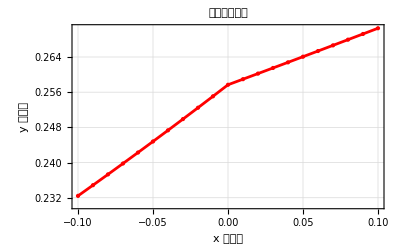

```mathematica
ListPlot[Transpose[{Δrlists,%}],PlotStyle->{Red,PointSize[Medium]},(*散点颜色和大小*)Joined->True,(*是否将点连接成线*)Mesh->All,(*在连线的同时显示原始数据点*)PlotRange->All,(*确保显示所有数据*)Frame->True,(*使用框架模式*)FrameLabel->{"x 轴标签","y 轴标签"},(*设置坐标轴名称*)PlotLabel->"数据图表标题",(*图表标题*)GridLines->Automatic                 (*添加网格线*)]
```

```mathematica
a[l,2]
```

1/(√2)

```mathematica
Re[N[ hilm[[2]]/.{l->1000,m->1000}/.parametersvalue/.{Δr->0.001,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]
```

General::munfl: 1.56211×10^-11 (-1.54686×10^-302+1.09402×10^-299 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: 1.95239×10^-9 (2.30409×10^-300-1.62956×10^-297 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: (6488510558591061 (0.00141393-0.999999 ⅈ))/(12533992214694839297218541322205806599077660936396643105114762304174660718737072240448517712248390084061466230544944771215«79»12443532632425743891629290357590205527073120733999903478468066891695971691449491944021911903436290379306521201737728000000) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

0.00119271

```mathematica
N[Re[hilm[[2]]/.{l->1000,m->1000}/.parametersvalue/.{Δr->0.001,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]
```

General::munfl: 1.56211×10^-11 (-1.54686×10^-302+1.09402×10^-299 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: 1.95239×10^-9 (2.30409×10^-300-1.62956×10^-297 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: (6488510558591061 (0.00141393-0.999999 ⅈ))/(12533992214694839297218541322205806599077660936396643105114762304174660718737072240448517712248390084061466230544944771215«79»12443532632425743891629290357590205527073120733999903478468066891695971691449491944021911903436290379306521201737728000000) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

0.00119271

```mathematica
hilm[[6]]
```

```mathematica
Manipulate[ListLinePlot[Transpose[{Δrlists,Re[N[hilm[[i]]/. parametersvalue/. {Δr->Δrlists,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]}],PlotRange->All,Frame->True,FrameLabel->{"Δr","Re[hilm[["<>ToString[i]<>"]]]"},PlotStyle->ColorData[97][i]],{i,1,10,1}]
```

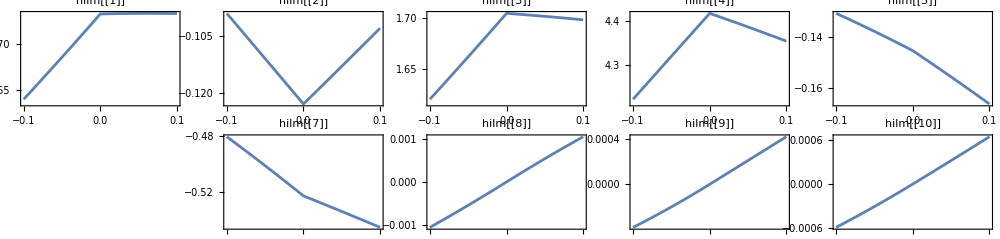

```mathematica
GraphicsGrid[Partition[Table[ListLinePlot[Transpose[{Δrlists,Re[N[hilm[[i]]/. parametersvalue/. {Δr->Δrlists,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]}],PlotLabel->"hilm[["<>ToString[i]<>"]]",PlotRange->All,Frame->True],{i,10}],5  (*每行5个*)],ImageSize->1000]
```

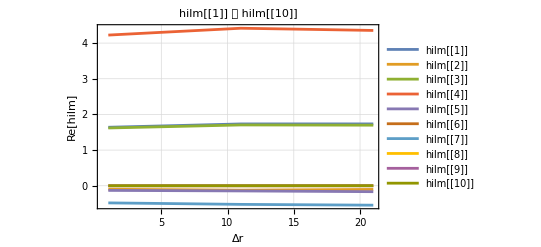

```mathematica
data=Table[Re[N[hilm[[i]]/. parametersvalue/. {Δr->Δrlists,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]],{i,10}];

ListLinePlot[data,PlotLegends->Table["hilm[["<>ToString[i]<>"]]",{i,10}],PlotRange->All,Frame->True,FrameLabel->{"Δr","Re[hilm]"},PlotLabel->"hilm[[1]] 到 hilm[[10]]",GridLines->Automatic]
```